```mathematica
Clear[j,n, u, p]
ϕ[j_,n_]:=2^n/(2 Pi Binomial[2n, n])(1+Cos[u-(2 Pi j)/(2n+1)])^n
T[j_,n_]:=Table[Exp[I (-2 Pi j p)/(2n+1)]Binomial[2n,n-p]/Binomial[2n,n],{p,-n,n}]
T[n_]:=Table[T[j,n],{j,0,2n}]
B[n_]:=Table[Exp[I k u]/(2 Pi),{k,-n,n}]
```

```mathematica
T[1,2].B[2]/.u->5//N
ϕ[1,2]/.u->5//N
```

0.00327417+0. ⅈ

0.00327417

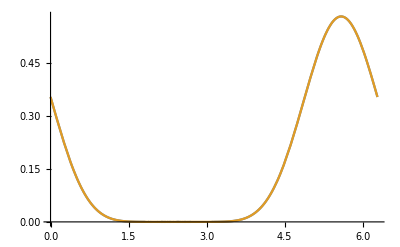

```mathematica
Plot[{T[-1,4].B[4],ϕ[-1,4]},{u,0,2Pi}]
```